```mathematica
Clear["Global`*"]
```

# Volume Integral Solver for RTE

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[sprtr,ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
If[$OperatingSystem=="MacOSX",sprtr="_";,0.0];
If[$OperatingSystem=="Windows",sprtr="_";,0.0];
If[$OperatingSystem=="Linux",sprtr="_";,0.0];

ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"mesh"}]
```

/Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

{True,True}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

directory created:/Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh/square26_dat

exported nodes file: /Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh/square26_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh/square26_dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh/trial_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/RTE2DVolumeIntegralSolver/mesh/trial_dat/triangles.dat

{True,True}

{0.,0.}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

Method1 - Full Matrix, Direct Solver
Compare Z1 and Z2

```mathematica
ClearAll[Z1,ZElemt1Fun,ZElemt1,TZ1,TZ1p]
(*ZElemt1Fun[{n_,m_},{np_,mp_}]:=If[n==np,If[m==mp,2N[π]area⟦n⟧(1+(musTbl⟦n⟧gTbl⟦m+Nd+1⟧-mutTbl⟦n⟧)√(area⟦n⟧/N[π])),0.0],area⟦n⟧area⟦np⟧(musTbl⟦np⟧gTbl⟦mp+Nd+1⟧-mutTbl⟦np⟧)Exp[-ⅈ(m-mp)r2rPhi⟦n,np⟧]/r2rR⟦n,np⟧]*)
ZElemt1Fun[{n_,m_},{np_,mp_}]:=If[n==np,If[m==mp,2N[π]area⟦n⟧(1+(mutTbl⟦np⟧-musTbl⟦np⟧gTbl⟦mp+Nd+1⟧)√(area⟦n⟧/N[π])),0.0],area⟦n⟧area⟦np⟧(mutTbl⟦np⟧-musTbl⟦np⟧gTbl⟦mp+Nd+1⟧)Exp[-ⅈ(m-mp)r2rPhi⟦n,np⟧]/r2rR⟦n,np⟧]
ZElemt1=ZElemt1Fun[{#1⟦1⟧,#1⟦2⟧},{#2⟦1⟧,#2⟦2⟧}]&;
TZ1=(Z1=Outer[ZElemt1[iLTbl⟦#1⟧,iLTbl⟦#2⟧]&,Range[Ng],Range[Ng]]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TZ1p=(Z1=ToCmplxPckdArry[Z1];)//AbsoluteTiming//#⟦1⟧&;
Print["{TZ1,TZ1p}=",{TZ1,TZ1p}//{Total[#],#}&];
Print["Z1=",PackedArrayQ[Z1]];

ClearAll[BlockZ,BlockV,NormZ]
BlockZ[{n1_,n2_},Z_]:=Z⟦iGTbl⟦n1,1⟧;;iGTbl⟦n1,Nm⟧,iGTbl⟦n2,1⟧;;iGTbl⟦n2,Nm⟧⟧
BlockV[n_,V_]:=V⟦iGTbl⟦n,1⟧;;iGTbl⟦n,Nm⟧⟧
NormZ=(#//Map[Norm,#]&//Total)&;

ClearAll[sol1,Tsol1,sol1p]
Tsol1=(sol1=LinearSolve[Z1,V];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol1=",Tsol1];
Print["Norm[Z1.sol1-V]/Norm[V]=",Norm[Z1.sol1-V]/Norm[V]];

sol1p=Partition[sol1,Nm];
Print["sym sol1=",Table[Norm[sol1p⟦n⟧-sol1p⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];

ClearAll[ShowV,ShowZ]
ShowV[V_]:=Partition[V,Nm]//Chop//TableForm
ShowZ[Z_]:=Partition[Z,{Nm,Nm}]//Chop//MatrixForm
X=ConstantArray[0.0,Ng];
X⟦1⟧=1.0;X[[1+Ns/2]]=1.0;
Z1//ShowZ;

ClearAll[Z3,n,np]
Z3=ConstantArray[0.0,{Ng,Ng}];
Z3=Partition[Z3,{Nm,Nm}];
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
If[n==np,Z3⟦n,np⟧=DiagonalMatrix[Zon1⟦n⟧+Zon2⟦n⟧gTbl],Z3⟦n,np⟧=Zoff⟦n,np⟧Outer[Times,vTblC⟦n,np⟧*,uTblC⟦n,np⟧]];
];
];
Z3//Chop//MatrixForm;

{Z1.X,ZDotXC[X],Z1.X-ZDotXC[X]}//Map[TableForm@Chop@#&,#]&;

Print["Norm[sol1-sol2]=",Norm[sol1-sol2]];
```

{TZ1,TZ1p}={0.23003,{0.21911,0.01093}}

Z1=True

Tsol1=0.00109

Norm[Z1.sol1-V]/Norm[V]=1.10665×10^-15

sym sol1=4.22283

Norm[sol1-sol2]=7.38759×10^-8

```mathematica
Z1p=Partition[Z1,{Nm,Nm}]//Chop;
Vp=Partition[V,Nm]//Chop;
Z1p⟦1,2⟧//Chop//MatrixForm;
Z1p⟦3,4⟧//Chop//MatrixForm;
Z1p⟦1,2⟧//Re//Chop//MatrixForm;
Z1p⟦3,4⟧//Re//Chop//MatrixForm;
Z1p⟦1,2⟧//Im//Chop//MatrixForm;
Z1p⟦3,4⟧//Im//Chop//MatrixForm;
Vp//MatrixForm;
Z1p⟦1,1⟧.Vp⟦1⟧-Z1p⟦3,3⟧.Vp⟦3⟧//Chop;
Z1p⟦1,2⟧.Vp⟦2⟧-Z1p⟦3,4⟧.Vp⟦4⟧//Chop;
Z1p⟦1,3⟧.Vp⟦3⟧-Z1p⟦3,1⟧.Vp⟦1⟧//Chop;
Z1p⟦1,4⟧.Vp⟦4⟧-Z1p⟦3,2⟧.Vp⟦2⟧//Chop;
```

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,f,f1,f2,func,func1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../script","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square948.msh"}];
DumpMSHFileTo2DATFiles[filename];
mus[{x_,y_}]:=0.1Log[2.0]
mua[{x_,y_}]:=Log[2.0]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.05;
f1[m_]:=g^Abs[m]
f2[m_]:=If[m==0,1.0,0.0]
f=f1;
func1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi])),CompilationTarget:>"C"];
func=func1;
phis=0.0;
Nd=50;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,AreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
r2rXYPreCalc[cntr_]:=Outer[If[#1<#2,Subtract@@cntr⟦{#1,#2}⟧,{0.0,0.0}]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#-#ᵀ&
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
r2rPhiPreCalc[cntr_]:=Outer[If[#1≠#2,(Subtract@@cntr⟦{#1,#2}⟧//ArcTan[#⟦1⟧,#⟦2⟧]&),0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray
r2rFPreCalc[r2rPhi_,phis_]:=Map[func[#-phis]&,r2rPhi,{2}];
AreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Abs//Divide[#,2.0]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=f/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rXY=(r2rXY=r2rXYPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rPhi=(r2rPhi=r2rPhiPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rF=(r2rF=Map[func[#-phis]&,r2rPhi,{2}];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=AreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}];
musTbl=mus/@cntr//ToPackedArray;
muaTbl=mua/@cntr//ToPackedArray;
mutTbl=musTbl+muaTbl;
Print["{musTbl,muaTbl,mutTbl}=",{musTbl,muaTbl,mutTbl}//Map[{PackedArrayQ[#],Rank[#]}&,#]&];


ClearAll[V,VRe,VIm,VElemtRe,VElemtIm,TVRe,TVIm]
VElemtRe=area⟦#⟦1⟧⟧Cos[#⟦2⟧phis]&;
VElemtIm=area⟦#⟦1⟧⟧Sin[#⟦2⟧phis]&;
VElemt=area⟦#⟦1⟧⟧Exp[-ⅈ#⟦2⟧phis]&;
TVRe=(VRe=1.0*VElemtRe[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TVIm=(VIm=1.0*VElemtIm[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
V=1.0*VRe-1.0ⅈ*VIm;
Print["{TVRe,TVIm}=",{TVRe,TVIm}//{Total[#],#}&];
Print["{V,VRe,VIm}=",PackedArrayQ/@{V,VRe,VIm}];
Print["Norm[V]=",Norm[V]];
```

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square948_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square948_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square948_dat/triangles.dat

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square948_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square948_dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={948,50,948,101,95748}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}={11.8559,{0.00036,0.00021,2.67223,2.74545,5.00993,1.42574,0.00202}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}={True,True,True,True,True,True,True}

{musTbl,muaTbl,mutTbl}={{True,{948,1}},{True,{948,1}},{True,{948,1}}}

{TVRe,TVIm}={0.74462,{0.38332,0.3613}}

{V,VRe,VIm}={True,True,True}

Norm[V]=0.327841

Method2 - Compressed Matrix, Iterative
Precalc

```mathematica
ClearAll[Zon1,Zon2,Zoff,vTblC,uTblC,TZon1,TZon2,TZoff,TvTblC,TuTblC]
TZon1=(Zon1=2π area+2 π^(1/2)mutTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZon2=(Zon2=-2 π^(1/2)musTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZoff=(Zoff=Outer[If[#2>#1,area⟦#1⟧area⟦#2⟧/r2rR⟦#1,#2⟧,0.0]&,Range[Ns],Range[Ns]]//ToPackedArray//#+#ᵀ&;)//AbsoluteTiming//#⟦1⟧&;

TvTblC=(vTblC=Compile[{{r2rPhi,_Real,2},{Ns,_Integer},{Nd,_Integer}},
Table[Exp[-ⅈ r2rPhi⟦n,np⟧Range[-Nd,Nd]],{n,Ns},{np,Ns}],
Parallelization->True
(*,CompilationTarget:>"C"*)
][r2rPhi,Ns,Nd];)//AbsoluteTiming//#⟦1⟧&;
TuTblC=(uTblC=Compile[{{musTbl,_Real,1},{mutTbl,_Real,1},{gTbl,_Real,1},{vTblC,_Complex,3},{r2rPhi,_Real,2},{Ns,_Integer}},
Table[mutTbl⟦np⟧vTblC⟦n,np⟧*-musTbl⟦np⟧gTbl vTblC⟦n,np⟧*,{n,Ns},{np,Ns}],
Parallelization->True
(*,CompilationTarget:>"C"*)
][musTbl,mutTbl,gTbl,vTblC,r2rPhi,Ns];
)//AbsoluteTiming//#⟦1⟧&;

Print["{TZon1,TZon2,TZoff,TvTblC,TuTblC}=",{TZon1,TZon2,TZoff,TvTblC,TuTblC}//{Total[#],#}&];
Print["{Zon1,Zon2,Zoff,vTblC,uTblC}=",PackedArrayQ/@{Zon1,Zon2,Zoff,vTblC,uTblC}];

(*
ClearAll[ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
Module[{Xp,Yp,temp,n,np},
Xp=Partition[X,2Nd+1];
Flatten@Table[
temp=ConstantArray[0.0+0.0ⅈ,2Nd+1];
For[np=1,np≤Ns,np++,
If[np==n,
temp+=Zon1⟦n⟧Xp⟦n⟧+Zon2⟦n⟧gTbl Xp⟦n⟧;,
temp+=Zoff⟦n,np⟧(Xp⟦np⟧.uTblC⟦n,np⟧)vTblC⟦n,np⟧;
];
];
temp
,{n,Ns}]
],
Parallelization->True
(*,CompilationTarget:>"C"*)
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#⟦1⟧&];
*)

ClearAll[ZDotXC0,ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC0=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
  Module[{Xp,Yp,temp,n,np},
    Xp=Partition[X,2Nd+1];
    Flatten@Table[
      temp=ConstantArray[0.0+0.0I,2Nd+1];
      For[np=1,np<=Ns,np++,
        If[np==n,
          temp+=Zon1[[n]]Xp[[n]]+Zon2[[n]]gTbl Xp[[n]];,
          temp+=Zoff[[n,np]](Xp[[np]].uTblC[[n,np]])vTblC[[n,np]];
        ];  
      ];  
      temp
      ,{n,Ns}]
  ],  
  Parallelization->True
  ,CompilationTarget:>"C"
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
ZDotXC[V_]:=Module[{},ZDotXCcounter++;ZDotXC0[V]]
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#[[1]]&];


ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
```

{TZon1,TZon2,TZoff,TvTblC,TuTblC}={12.4349,{0.00009,0.00005,2.12187,6.59571,3.71717}}

{Zon1,Zon2,Zoff,vTblC,uTblC}={True,True,True,True,True}

ZDotXC[V] time=1.55921

Solution with the old V_(n m)

Tsol2=11.63659

Norm[ZDotXC[sol2]-V]/Norm[V]=5.83184×10^-9

Norm[ZDotXC[sol2]-V]/Norm[V]=9.49844×10^-10

sym sol2=3.81949

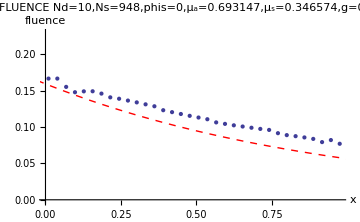

```mathematica
ClearAll[sol2,Tsol2,sol2p]
Tsol2=(sol2=LinearSolve[ZDotXC,V,Method->{"Krylov",Tolerance->Norm[V]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2=",Tsol2];
Print["Norm[ZDotXC[sol2]-V]/Norm[V]=",Norm[ZDotXC[sol2]-V]/Norm[V]];
Print["Max[Norm/@(ZDotXC[sol2]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2]-V)]/Norm[V]];
sol2p=Partition[sol2,Nm];
Print["sym sol2=",Table[Norm[sol2p⟦n⟧-sol2p⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];

ClearAll[A,y,CoordTbl,nTbl,pltstr,fluence]
sol2p=Partition[sol2,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
pltstr="OLD FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[Transpose@{CoordTbl⟦All,1⟧,sol2p⟦nTbl,Nd+1⟧//Re},PlotRange->{0,1/(2π)+0.07},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[With[{mutt=mut[{0,0}],muaa=mua[{0,0}],muss=mus[{0,0}]},Exp[-mutt(x)]/(2π)],{x,-1,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2p⟦All,Nd+1⟧}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y],{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet;
```

(V_sc)_(n m) (needs V_(n m) as input) and solve

```mathematica
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-7&&Abs[ds⟦3⟧]<1.0*10^-7),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
If[t⟦1⟧<0.0,t⟦1⟧=0.0;,0.0;];
If[t⟦2⟧<0.0,t⟦2⟧=0.0;,0.0;];
t⟦2⟧-t⟦1⟧
]
(*,CompilationTarget:>"C"*)
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];

ClearAll[damp,Tdamp1,damp1]
Tdamp1=(damp1=Exp[-mutTbl⟦1⟧cntr⟦All,1⟧];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp1=",Tdamp1];
Print["damp1=",damp1//PackedArrayQ];

ClearAll[OpticalPathC,damp2C,Tdamp2C]
OpticalPathC=Compile[{{P0,_Real,1},{phi,_Real},{mutTbl,_Real,1},{pt,_Real,3},{Ns,_Integer}},
(*Total[Table[mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧],{np,1,Ns}]]*)
Module[{np,tau=0.0},For[np=1,np≤Ns,np++,tau+=mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧];];tau]
][#1,#2,mutTbl,pt,Ns]&;

Tdamp2C=(damp2C=Exp[Table[-OpticalPathC[cntr⟦n⟧,phis+π],{n,Ns}]];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp2C=",Tdamp2C]
Print["damp2C=",damp2C//PackedArrayQ];
Print["Norm[damp2C-damp1]=",Norm[damp2C-damp1]]

damp=damp2C;
```

Tdamp1=0.00004

damp1=True

Tdamp2C=9.717038

damp2C=True

Norm[damp2C-damp1]=1.82513×10^-15

```mathematica
ClearAll[Von,Voff,Vsc,TVsc]
TVsc=(
Von=musTbl √(area/π)damp;
Voff=((Zoff r2rF)ᵀ(damp musTbl))ᵀ;
Vsc=Von(Partition[V,Nm]ᵀg)ᵀ;
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
Vsc⟦n⟧+=Voff⟦n,np⟧vTblC⟦n,np⟧;
];
];
Vsc=Flatten[Vsc];)//AbsoluteTiming//#⟦1⟧&;
Print["Vsc=",PackedArrayQ[Vsc]];
Print["TVsc=",TVsc];
```

Vsc=True

TVsc=7.73785

```mathematica
ClearAll[sol2sc,Tsol2sc,sol2scp]
Tsol2sc=(sol2sc=LinearSolve[ZDotXC[#]&,Vsc,Method->{"Krylov",Tolerance->Norm[Vsc]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2sc=",Tsol2sc];
Print["Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=",Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]];
Print["Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2sc]-Vsc)]/Norm[Vsc]];
sol2scp=Partition[sol2sc,Nm];
Print["sym sol2sc=",Table[Norm[sol2scp⟦n⟧-sol2scp⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];
Print["Nd residual=",(sol2scp⟦All,1⟧//Map[Norm,#]&//Norm)/(sol2scp⟦All,Nd+1⟧//Map[Norm,#]&//Norm)];
```

Tsol2sc=37.76487

Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=7.26854×10^-11

Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=2.19708×10^-11

sym sol2sc=0.0623445

Nd residual=0.0326787

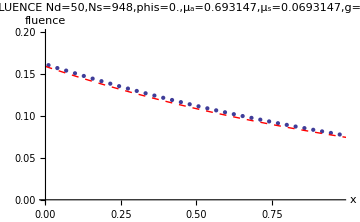

```mathematica
ClearAll[A,y,CoordTbl,nTbl,data,n,pltstr,fluence]
sol2scp=Partition[sol2sc,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
data=Transpose@{CoordTbl⟦All,1⟧,sol2scp⟦nTbl,Nd+1⟧//Re};
For[n=1,n≤Length[data],n++,data⟦n,2⟧+=Exp[-OpticalPathC[CoordTbl⟦n⟧,phis+π]]/(2π);];
pltstr="NEW FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[data,PlotRange->{0,1/(2π)+0.04},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[Exp[-mut[{0.,0.}]x]/(2π),{x,0,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2scp⟦All,Nd+1⟧32}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y]+Exp[-mutTbl⟦1⟧x]/(2π),{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet
```

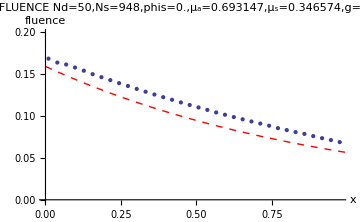

-Graphics-

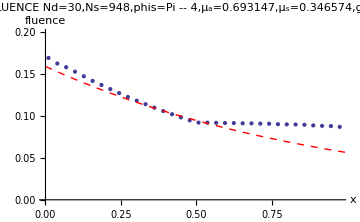

-Graphics-

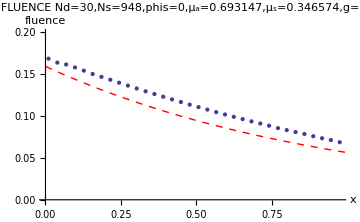

-Graphics-

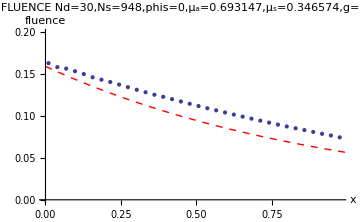

-Graphics-

```mathematica
-Graphics-›
```

Save & Read - OLD

```mathematica
ClearAll[SaveSolution] 
SaveSolution[filename_,Nd_,phis_,sol_]:=Module[{soldir}, 
  soldir=DirectoryName[filename]<>FileBaseName[filename]<>sprtr<>"sol"<>"Nd"<>ToString[Nd]<>"phis"<>ToString[phis]; 
  CreateDirectory[soldir]//Quiet; 
  {Export[FileNameJoin[{soldir,"niter+time"}],{ZDotXCcounter,Tsol2t},"Table"] 
  ,Export[FileNameJoin[{soldir,"re.dat"}],N@Re[sol]] 
  ,Export[FileNameJoin[{soldir,"im.dat"}],N@Im[sol]]}//Parallelize//Quiet; 
] 
Print["save solution time=",SaveSolution[filename,Nd,phis,sol2sc]//AbsoluteTiming//#[[1]]&]; 
ClearAll[ReadSolution,sol2scr] 
ReadSolution[filename_,Nd_,phis_]:=Module[{soldir}, 
  soldir=DirectoryName[filename]<>FileBaseName[filename]<>sprtr<>"sol"<>"Nd"<>ToString[Nd]<>"phis"<>ToString[phis]; 
  {Import[FileNameJoin[{soldir,"niter+time"}],"Table"]//ToPackedArray//Flatten 
  ,Import[FileNameJoin[{soldir,"re.dat"}]]+I*Import[FileNameJoin[{soldir,"im.dat"}]]//Flatten} 
] 
ClearAll[niter,Tsol] 
Print["read solution time=",({{niter,Tsol},sol2scr}=ReadSolution[filename,Nd,phis];)//AbsoluteTiming//#[[1]]&];
sol2scr=sol2scr//ToCmplxPckdArry;
Print["{nitr,Tsol}=",{niter,Tsol}]; 
Print["sol2scr=",sol2scr//PackedArrayQ]
```

save solution time=0.38079

read solution time=0.42415

{nitr,Tsol}={22,Tsol2t}

sol2scr=True

Save & Read

```mathematica
ClearAll[SolDirName,NsList,NdList,phis,filenameList,solList,geo]
SolDirName[Ns_,Nd_,phis_,geo:"square"]:=FileNameJoin[{NotebookDirectory[],"../msh","square"<>ToString[Ns]<>sprtr<>"solNd"<>ToString[Nd]<>"phis"<>ToString[phis]}];
NsList={26,42,90,162,242,346,518,614,782,948,1126,1384};
NdList=Range[10,110,10];
{NNs,NNd}=Length/@{NsList,NdList};
phis=0;
geo="square";
filenameList=Table[FileNameJoin[{NotebookDirectory[],"../msh","square"<>ToString[Ns]<>".msh"}],{Ns,NsList}];
Print["read all solution time=",(solList=ParallelTable[ReadSolution[filenameList⟦iNs⟧,Nd,phis],{iNs,NNs},{Nd,NdList}];)//AbsoluteTiming//#⟦1⟧&];
Print["solList=",N[ByteCount[solList]/2^20],"MB"];
```

$Aborted

solList=0.MB

Convergence accuracy

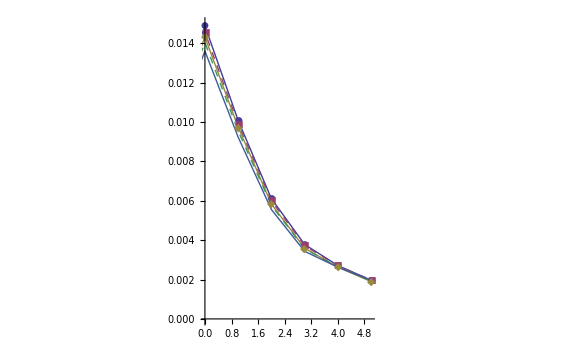

```mathematica
(*
ClearAll[nsRange,ndRange,style,iNs,iNd,n]
{iNs,iNd,n}={4,9,PickTriangle[{0.9,0.5}]};
nsRange=Range[9,NNs,1];
ndRange=Range[1,NNd,2];
style={{Thick,Dashed},{Thick}};
ParallelTable[{Range[-NdList⟦iNd⟧,NdList⟦iNd⟧],Abs@Partition[solList⟦iNs,iNd,2⟧//Chop,2*NdList⟦iNd⟧+1]⟦n⟧}ᵀ,{iNs,nsRange}]//ListLinePlot[#,PlotRange->{0,0.006},PlotStyle->style,ImageSize->Large,AxesLabel->{"m","|V_(n m)|"},PlotLabel->"Specific intensity |V_(n m)| vs. Ns\nNd="<>ToString[NdList⟦iNd⟧]<>",n="<>ToString[n]<>",{x,y}="<>ToString[cntr⟦n⟧],PlotLegends->Placed[NsList⟦nsRange⟧,{0.7,0.7}]]&
*)
ClearAll[nsRange,ndRange,style,pltstr,iNs,iNd,n]
{iNs,iNd,n}={12,7,390};
nsRange=Range[9,NNs,1];
ndRange=Range[3,NNd,2];
style={{Medium},{Medium,Dashed}};
pltstr="Specific intensity |V_(n m)| vs. Nd\nNs="<>ToString[NsList⟦iNs⟧]<>",n="<>ToString[n];

Show[
ParallelTable[{Range[-NdList⟦iNd⟧,NdList⟦iNd⟧],Abs@Partition[solList⟦iNs,iNd,2⟧//Chop,2*NdList⟦iNd⟧+1]⟦n⟧}ᵀ,{iNd,ndRange}]//ListLinePlot[#,PlotRange->{{0,5},{0,0.015}},PlotStyle->style,ImageSize->Large,AxesLabel->{"m","|V_(n m)|"},PlotLabel->pltstr,PlotLegends->Placed[NdList⟦ndRange⟧,{0.5,0.7}],PlotMarkers->Automatic]&
(*,ListPlot[Table[{m,0.016 g^Abs[m]},{m,-110,110}],Joined->True,PlotStyle->{Red,Dashed}]*)
]
```

Plot: niter, time - Ns, Nd

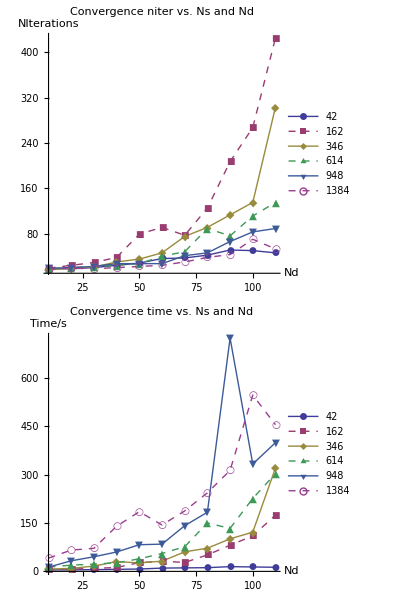

```mathematica
ClearAll[range,style]
range=Range[2,NNs,2];
style={{Thick},{Thick,Dashed}};
Print@Grid[{{
ParallelTable[{NdList,solList⟦iNs,All,1,1⟧}ᵀ,{iNs,range}]//ListLinePlot[#,PlotLegends->Placed[NsList⟦range⟧,{0.4,0.7}],PlotStyle->style,AxesOrigin->{10,10},PlotRange->All,ImageSize->Large,AxesLabel->{"Nd","NIterations"},PlotMarkers->Automatic,PlotLabel->"Convergence niter vs. Ns and Nd"]&},
{ParallelTable[{NdList,solList[[iNs,All,1,2]]}ᵀ,{iNs,range}]//ListLinePlot[#,PlotLegends->Placed[NsList⟦range⟧,{0.4,0.7}],PlotStyle->style,AxesOrigin->{10,0},PlotRange->All,ImageSize->Large,AxesLabel->{"Nd","Time/s"},PlotMarkers->Automatic,PlotLabel->"Convergence time vs. Ns and Nd"]&
}}]
```